## 5. Labor

## 1.feladat

Function[{x},0.5 Cos[x]]

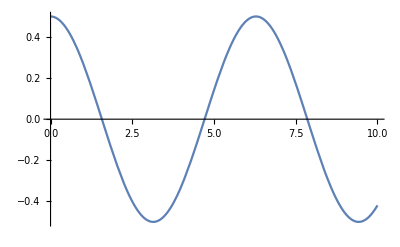

```mathematica
m=1;
k=1;
x0=0.5;
soly=DSolveValue[{m*y''[x]==-k*y[x],y'[0]==0,y[0]==x0},y,{x,0,10}]

Plot[soly[x],{x,0,10}]

springWithBall[x_]:={Line[Join[{{-1,0},{-1,0}+1/20 {x+1,0}},Table[{-1,0}+n/10 {x+1,0}-(-1)^n*1/10 {0,1},{n,1,8}],{(1-3/20)*{x+1,0}+{-1,0},{x,0}}]],{Red,Ball[{x,0},0.1]}};


Animate[Graphics[springWithBall[soly[x]],PlotRange->{{-1,1},{-0.5,0.5}},Axes->True],{x,0,10}]
```

## 2. feladat

```mathematica
megoldasok=NDSolveValue[{
x1''[t]==(x2[t]-x1[t])/((x2[t]-x1[t])^2+(y2[t]-y1[t])^2)^(3/2),
y1''[t]==(y2[t]-y1[t])/((x2[t]-x1[t])^2+(y2[t]-y1[t])^2)^(3/2),
x1[0]==0,x1'[0]==0,y1[0]==0,y1'[0]==0,
x2''[t]==300*(x1[t]-x2[t])/((x2[t]-x1[t])^2+(y2[t]-y1[t])^2)^(3/2),
y2''[t]==300*(y1[t]-y2[t])/((x2[t]-x1[t])^2+(y2[t]-y1[t])^2)^(3/2),
x2[0]==100,x2'[0]==0,y2[0]==0,y2'[0]==1},
{x1,y1,x2,y2},{t,0,200}];

mx1=megoldasok[[1]];
my1=megoldasok[[2]];
mx2=megoldasok[[3]];
my2=megoldasok[[4]];

Animate[
Show[
ParametricPlot[{mx1[t],my1[t]},{t,0,t0},PlotRange->All],
ParametricPlot[{mx2[t],my2[t]},{t,0,t0},PlotRange->All],
Graphics[{Red,Disk[{mx1[t0],my1[t0]}]}],
Graphics[{Red,Disk[{mx2[t0],my2[t0]}]}]],
{t0,0,200},
SaveDefinitions->True
]
```